Part::partw: Part 2 of eigmods[k] does not exist.

Part::partw: Part 3 of eigmods[k] does not exist.

Part::partw: Part 4 of eigmods[k] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

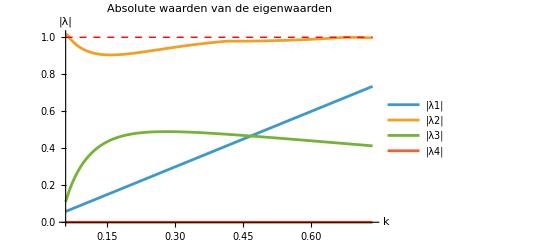

General::munfl: 1/((-8.54854×10^21)^18) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((-1.01908×10^22)^18) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((-7.04267×10^20)^18) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

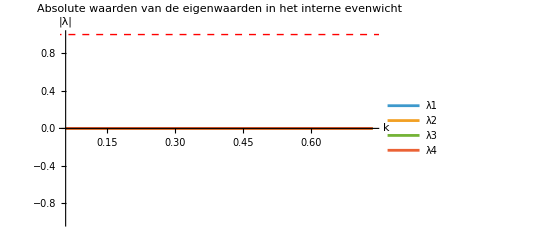

```mathematica
ClearAll["Global`*"]

hDval=0.3;
hSval=1;
csupval=0.15;

vars={x00,x01,x10,x11};

tfun[k_?NumericQ]:=0.87*k;
ctfun[k_?NumericQ]:=0.9*k^(3/2);

pstar[k_?NumericQ]:=Module[{ct,tt},ct=ctfun[k];
tt=tfun[k];
hDval*(ct*(1+hDval*tt)-tt)/(ct*(2*hDval-1))];

f00=x00^2+x00*x01+(1-hD*t)*(1-hD*ctrait)*x00*x10+1/2*(1-hD*(1-hS)*t)*(1-hD*(1-hS)*ctrait-hS*csup)*x00*x11+1/2*(1-hD*(1-hS)*t)*(1-hD*(1-hS)*ctrait-hS*csup)*x01*x10;

f01=x00*x01+1/2*(1-hD*(1-hS)*t)*(1-hD*(1-hS)*ctrait-hS*csup)*x00*x11+x01^2+1/2*(1-hD*(1-hS)*t)*(1-hD*(1-hS)*ctrait-hS*csup)*x01*x10+(1-csup)*x01*x11;

f10=(1+hD*t)*(1-hD*ctrait)*x00*x10+1/2*(1+hD*(1-hS)*t)*(1-hD*(1-hS)*ctrait-hS*csup)*x00*x11+1/2*(1+hD*(1-hS)*t)*(1-hD*(1-hS)*ctrait-hS*csup)*x01*x10+(1-ctrait)*x10^2+(1-(1-hS)*ctrait-hS*csup)*x10*x11;

f11=1/2*(1+hD*(1-hS)*t)*(1-hD*(1-hS)*ctrait-hS*csup)*x00*x11+1/2*(1+hD*(1-hS)*t)*(1-hD*(1-hS)*ctrait-hS*csup)*x01*x10+(1-csup)*x01*x11+(1-(1-hS)*ctrait-hS*csup)*x10*x11+(1-csup)*x11^2;

w=f00+f01+f10+f11;

F={f00/w,f01/w,f10/w,f11/w};


J=D[F,{vars}];

Jeq[k_?NumericQ]:=N[J/. {x00->1-pstar[k],x01->0,x10->pstar[k],x11->0,hD->hDval,hS->hSval,csup->csupval,t->tfun[k],ctrait->ctfun[k]},30];

eigs[k_?NumericQ]:=Eigenvalues[Jeq[k]];

eigmods[k_?NumericQ]:=Abs[eigs[k]];

Plot[Evaluate[Table[eigmods[k][[i]],{i,1,4}]],{k,0.058109,0.734631},PlotRange->All,PlotLegends->{"|λ1|","|λ2|","|λ3|","|λ4|"},AxesLabel->{"k","|λ|"},PlotLabel->"Absolute waarden van de eigenwaarden",Epilog->{Red,Dashed,Line[{{0.058109,1},{0.734631,1}}]}]
```

```mathematica
ClearAll["Global`*"]

cTrait[k_]:=0.9 k^(3/2);
cSup=0.15;
t[k_]:=0.87 k;

f00=x00^2+x00 x01+(1-cTrait[k] hD) (1-hD t[k]) x00 x10+1/2 (1-cTrait[k] hD (1-hS)-cSup hS) (1-hD (1-hS) t[k]) x01 x10+1/2 (1-cTrait[k] hD (1-hS)-cSup hS) (1-hD (1-hS) t[k]) x00 x11;

f01=x00 x01+x01^2+1/2 (1-cTrait[k] hD (1-hS)-cSup hS) (1-hD (1-hS) t[k]) x01 x10+1/2 (1-cTrait[k] hD (1-hS)-cSup hS) (1-hD (1-hS) t[k]) x00 x11+(1-cSup) x01 x11;

f10=(1-cTrait[k] hD) (1+hD t[k]) x00 x10+1/2 (1-cTrait[k] hD (1-hS)-cSup hS) (1+hD (1-hS) t[k]) x01 x10+(1-cTrait[k]) x10^2+1/2 (1-cTrait[k] hD (1-hS)-cSup hS) (1+hD (1-hS) t[k]) x00 x11+(1-cTrait[k] (1-hS)-cSup hS) x10 x11;

f11=1/2 (1-cTrait[k] hD (1-hS)-cSup hS) (1+hD (1-hS) t[k]) x01 x10+1/2 (1-cTrait[k] hD (1-hS)-cSup hS) (1+hD (1-hS) t[k]) x00 x11+(1-cSup) x01 x11+(1-cTrait[k] (1-hS)-cSup hS) x10 x11+(1-cSup) x11^2;

wbar=Expand[f00+f01+f10+f11];

g00=Together[f00/wbar];
g01=Together[f01/wbar];
g10=Together[f10/wbar];
g11=Together[f11/wbar];

J=D[{g00,g01,g10,g11},{{x00,x01,x10,x11}}];

Jint=Simplify[J/. {x00->0.8335756742,x01->0.1664243258,x10->0,x11->0, hD -> 0.4, hS -> 0.5, k -> 0.5}];

MatrixForm[Jint]
```

(0.166424 | -0.833576 | -0.785468 | -1.1051
-0.166424 | 0.833576 | -0.224415 | 0.183158
0. | 0. | 0.931972 | 0.390238
0. | 0. | 0.0779114 | 0.531699)

```mathematica
Eigenvalues[Jint]
```

{1.,0.997275,0.466395,0.}